```mathematica
f[x_]:= Piecewise[{{1+Cos[x*π], Abs[x]≤ 1}}]
y[x_] := ⅇ^(-3*Abs[x])*Sin[2x]
```

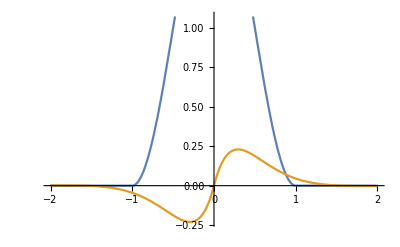

```mathematica
Plot[{f[x], y[x]}, {x, -2,2}]
```

```mathematica
pr = ∫_(-∞)^∞ Abs[y[x]]ⅆx
```

(4+6 ⅇ^(3 π/2)+4 ⅇ^(3 π)-Csch[(3 π)/2]+ⅇ^(3 π) Csch[(3 π)/2])/(13 (-1+ⅇ^(3 π/2)) (1+ⅇ^(3 π/2)))

```mathematica
g[w_]:=√(2/π)∫_0^∞ (f[x]Cos[w*x])ⅆx
```

```mathematica
m[w_]:=√(2/π)∫_0^∞ (f[x]Sin[w*x])ⅆx
```

```mathematica
ff=1/(√(2*π))∫_0^10 (g[w]Cos[w*x]+m[w]Sin[w*x])ⅆw
```

1/(2 π)(-CosIntegral[-(-10+π) (-1+x)] Sin[π x]+CosIntegral[-(10+π) (-1+x)] Sin[π x]+CosIntegral[(-10+π) x] Sin[π x]-CosIntegral[(10+π) x] Sin[π x]-Log[1-x] Sin[π x]+Log[-1+x] Sin[π x]-Log[-x] Sin[π x]+Log[x] Sin[π x]+2 SinIntegral[10-10 x]+Cos[π x] SinIntegral[(-10+π) (-1+x)]+2 SinIntegral[10 x]-Cos[π x] SinIntegral[(-10+π) x]+Cos[π x] SinIntegral[(10+π) x]+Cos[π x] SinIntegral[10+π-10 x-π x])

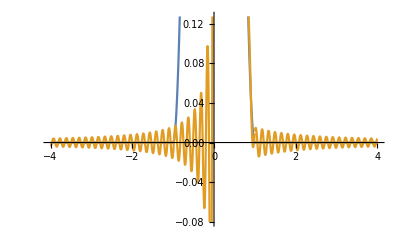

```mathematica
Plot[{f[x], ff}, {x, -4,4}]
```

```mathematica
ff1[w_] := √(2*π) *ⅇ^(-2Abs[w])
```

```mathematica
ff2[w_]:=Cos[4*π + π/3]
```

```mathematica
ff3[w_]:= (2*Cos[3(w*2*π)])/(w-2*π)
```